```mathematica
$ProcessorCount
LaunchKernels[]
```

8

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

```mathematica
(*E:\\mingw-w64\\x86_64-8.1.0-posix-seh-rt_v6-rev0\\mingw64*)
Needs["CCompilerDriver`GenericCCompiler`"]
$CCompiler={"Compiler"->GenericCCompiler,"CompilerInstallation"->"E:\\mingw-w64\\x86_64-8.1.0-posix-seh-rt_v6-rev0\\mingw64","CompilerName"->"x86_64-w64-mingw32-gcc.exe"};
<<CompiledFunctionTools`
```

```mathematica
(*тензор диэлектрической проницаемости*)
```

```mathematica
mee=SetPrecision[0.511 10^6,MachinePrecision];
qc=1/mee;

With[{ωp=ωp},
ϵpp=Compile[{{k0,_Real}},2.4
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*перпендикулярная диэлектрическая проницаемость. ϵ3*)
ϵav=Compile[{{k0,_Real}},Evaluate[(2.4+2.9)/2]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*средняя диэлектрическая проницаемость. ϵ*)
Ah=Compile[{{k0,_Real}},Evaluate[(2.9-2.4)/4]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];
Ahc=Compile[{{k0,_Real}},Evaluate[Conjugate[(2.9-2.4)/4]]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];
(*комплексная анизотропия. A*)
αh=Compile[{{k0,_Real}},Evaluate[N[1/10]]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];
αhc=Compile[{{k0,_Real}},Evaluate[Conjugate[1/10]]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*комплексная биаксиальность. α*)
βh=Compile[{{k0,_Real}},Evaluate[N[1/20]]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];
βhc=Compile[{{k0,_Real}},Evaluate[Conjugate[N[1/20]]]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*комплексная биаксиальность. β*)
yh=Compile[{{k0,_Real}},Evaluate[N[1/100]]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"](*гиротропность. y*);
]
```

```mathematica
(*блочная матрица*)
```

```mathematica
pp=2;(*2p+1-волновое приближение*)
```

```mathematica
Module[{U0,U1,bcV1,bsVb,k0sV0,eqs,ceq1,ceq2,t,eh1,eh2,ap,am,p3},
U0={{1+kp^2/2/k3bs,kp^2/2/k3bs},{kp^2/2/k3bs,1+kp^2/2/k3bs}};
U1=2 {{bc t+b/t,(ac+bc) t},{(a+b)/t,a/t+ac t}};
bcV1=2 {{b/t,-ac t},{b/t,-ac t}};
bsVb=4 {{b bc,ac bc t^2},{a b/t^2,a ac}};
k0sV0={{(ep-y) k0s-kp^2/2,kp^2/2+Ac k0s t^2},{kp^2/2+A k0s/t^2,(ep+y) k0s-kp^2/2}};

eqs=(-p3^2 U0-kp k0s/(2 k3bs) p3 U1+k0sV0+k0s kp/(2 k3bs) bcV1-k0s^2/(2 k3bs) bsVb).{ap[p3],am[p3]};

ceq1=CoefficientList[t^2 eqs[[1]],t];
ceq2=CoefficientList[t^2 eqs[[2]],t];

eh1[n_]:=Collect[Total[MapIndexed[(#1/.(p3->p3-(First[#2]-3)))&,ceq1]],{ap[_],am[_]},FullSimplify]/.{p3->qn+n};
eh2[n_]:=Collect[Total[MapIndexed[(#1/.(p3->p3-(First[#2]-3)))&,ceq2]],{ap[_],am[_]},FullSimplify]/.{p3->qn+n-2};
MMV[p_]:=Module[{Polys,Elems},
Polys={};
Elems={};
Do[
AppendTo[Polys,eh1[-i]==0];
AppendTo[Polys,eh2[-i]==0];
AppendTo[Elems,ap[-i+qn]];
AppendTo[Elems,am[-i+qn-2]];
,{i,-p,p}];

CoefficientArrays[Polys,Elems][[2]]//Normal
]
]
```

```mathematica
mmi[p_]:=Drop[Drop[MMV[p],-1,-1],1,1]
```

```mathematica
If[FailureQ[FindFile[NotebookDirectory[]<>"DisperHelDet"<>ToString[pp]<>".dat"]]==True,
dspp=If[pp≤5,
Module[{ii,cl,cll,det},
det=Det[mmi[pp]];
cl=CoefficientList[det,qn];
cll=Length[cl];
cl=ParallelMap[Simplify,cl,Method->"FinestGrained"];
det=0;
Do[det+=cl[[ii]] qn^(ii-1),{ii,1,cll}];
det]
,Collect[Det[mmi[pp]],qn]];(*дисперсионнный определитель. если есть, то загружается из файла*)
Put[dspp,NotebookDirectory[]<>"DisperHelDet"<>ToString[pp]<>".dat"];,
dspp=Get[NotebookDirectory[]<>"DisperHelDet"<>ToString[pp]<>".dat"];]

mmieq=mmi[pp];(*матрица уравнения*)
```

```mathematica
dsp[k0s1_?NumberQ,kp1_?NumberQ,k3bs1_?NumberQ,Aa1_?NumberQ,Aa1c_?NumberQ,a1_?NumberQ,a1c_?NumberQ,b1_?NumberQ,b1c_?NumberQ,y1_?NumberQ,ep1_?NumberQ,qn1_]=dspp/.{k0s->k0s1,kp->kp1,k3bs->k3bs1,qn->qn1,A->Aa1,Ac->Aa1c,a->a1,ac->a1c,b->b1,bc->b1c,y->y1,ep->ep1};
meq=Compile[{{k0s1,_Real},{kp1,_Real},{k3bs1,_Real},{Aa1,_Complex},{Aa1c,_Complex},{a1,_Complex},{a1c,_Complex},{b1,_Complex},{b1c,_Complex},{y1,_Real},{ep1,_Real},{qn1,_Complex}},Evaluate[mmieq/.{k0s->k0s1,kp->kp1,k3bs->k3bs1,qn->qn1,A->Aa1,Ac->Aa1c,a->a1,ac->a1c,b->b1,bc->b1c,y->y1,ep->ep1}]
,RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*функции для определителя и матрицы*)
```

```mathematica
PolynomialQ[dspp,qn]
```

True

```mathematica
mmi[2]/.kp-> 0//MatrixForm
```

(-(4 a ac k0s^2+2 k3bs qn^2-2 k0s k3bs (ep+y))/(2 k3bs) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(4 b bc k0s^2-2 ep k0s k3bs+2 k3bs (1+qn)^2+2 k0s k3bs y)/(2 k3bs) | k0s (Ac-(2 ac bc k0s)/k3bs) | 0 | 0 | 0 | 0 | 0
0 | k0s (A-(2 a b k0s)/k3bs) | -(4 a ac k0s^2+2 k3bs (-1+qn)^2-2 k0s k3bs (ep+y))/(2 k3bs) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(4 b bc k0s^2-2 ep k0s k3bs+2 k3bs qn^2+2 k0s k3bs y)/(2 k3bs) | k0s (Ac-(2 ac bc k0s)/k3bs) | 0 | 0 | 0
0 | 0 | 0 | k0s (A-(2 a b k0s)/k3bs) | -(4 a ac k0s^2+2 k3bs (-2+qn)^2-2 k0s k3bs (ep+y))/(2 k3bs) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(4 b bc k0s^2-2 ep k0s k3bs+2 k3bs (-1+qn)^2+2 k0s k3bs y)/(2 k3bs) | k0s (Ac-(2 ac bc k0s)/k3bs) | 0
0 | 0 | 0 | 0 | 0 | k0s (A-(2 a b k0s)/k3bs) | -(4 a ac k0s^2+2 k3bs (-3+qn)^2-2 k0s k3bs (ep+y))/(2 k3bs) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(4 b bc k0s^2-2 ep k0s k3bs+2 k3bs (-2+qn)^2+2 k0s k3bs y)/(2 k3bs))

```mathematica
CheckEigenVector[eigv_]:=Module[{res=False,p,prev,cur,k},
p=pp;
If[Length[eigv]==4p,res=True];
prev=Abs[eigv[[1]]]^2+Abs[eigv[[4p]]]^2;
For[k=0,k<p-1,k++,
If[res,
cur=Abs[eigv[[1+2k+1]]]^2+ Abs[eigv[[1+2k+2]]]^2 + Abs[eigv[[4p-(2k+1)]]]^2+Abs[eigv[[4p-(2k+2)]]]^2;
If[cur<prev, res=False];
prev=cur;

]
];
cur=Abs[eigv[[2p]]]^2+Abs[eigv[[2p+1]]]^2;
If[res,If[cur< prev,res=False]];
res
]
```

```mathematica
CheckEigenVector[{0,1,2,3,1,2,1,0}]
```

0

10

10

True

```mathematica
ChoiceMainBranch=Compile[{{p,_Integer},{k0s,_Real},{kp,_Real},{k3bs,_Real},{Aa,_Complex},{Aac,_Complex},{a,_Complex},{ac,_Complex},{b,_Complex},{bc,_Complex},{y,_Real},{ϵ,_Real},{rts,_Complex,1}},Module[{i,j,k,nmax,ff,rtss,mm1,mm1n,eigv,eigv1,eigvr,partnorm,nv1,crit=0.5},
Do[
rtss=rts[[i]];
mm1n=meq[k0s,kp,k3bs,Aa,Aac,a,ac,b,bc,y,ϵ,rtss];
eigv=NullSpace[mm1n];
Do[
eigv1=eigv[[k]];
nv1=Norm[eigv[[k]]];
eigv1=eigv1/nv1;
partnorm=Abs[eigv1[[2 p]]]^2+Abs[eigv1[[2 p+1]]]^2+Abs[eigv1[[2 p-3]]]^2;(*+Abs[eigv1[[2 p-1]]]^2*)
If[CheckEigenVector[eigv1],
eigvr=Append[eigv1,rtss];
Sow[eigvr];](*записываем в стек (СВ,СЗ), СЗ -- последний элемент с номером 4p+1*);
,{k,1,Length[eigv]}];
,{i,1,Length[rts]}];
],{{NullSpace[_],_Complex,2},{Length[_],_Integer},{Norm[_],_Real},{meq[_,_,_,_,_,_,_,_,_,_,_],_Complex,2},{Sow[_],_Complex,1}},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"];

Branches[p_?NumberQ,k0s_?NumberQ,kp_?NumberQ,k3bs_?NumberQ,Aa_?NumberQ,Aac_?NumberQ,a_?NumberQ,ac_?NumberQ,b_?NumberQ,bc_?NumberQ,y_?NumberQ,ϵ_?NumberQ]:=Module[{rts,ddsp,q1,bb},
ddsp=dsp[k0s,kp,k3bs,Aa,Aac,a,ac,b,bc,y,ϵ,q1];
rts=q1/.{ToRules[NRoots[ddsp==0,q1,PrecisionGoal->30]]};
bb=Reap[ChoiceMainBranch[p,k0s,kp,k3bs,Aa,Aac,a,ac,b,bc,y,ϵ,rts]];
Last[bb][[1]]];
```

```mathematica
SetSharedFunction[ParallelSow]
ParallelSow[ex_]:=Sow[ex];
```

```mathematica
With[{qc=qc},
DisperMain[p_?IntegerQ,kp_?NumberQ,k3bs_?NumberQ,Aa_?NumberQ,Aac_?NumberQ,a_?NumberQ,ac_?NumberQ,b_?NumberQ,bc_?NumberQ,y_?NumberQ,ϵ_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]:=Module[{k00,k0,k0ie,k0fe,dk0e,kpe,k3bse,Aae,Aace,ae,ace,be,bce,ye,ϵe},
k0ie=SetPrecision[k0i,Infinity];
k0fe=SetPrecision[k0f,Infinity];
dk0e=SetPrecision[dk0,Infinity];
kpe=SetPrecision[kp,Infinity];
k00=k0 qc;
k3bse=SetPrecision[ϵpp[k00] k0^2-kp^2,Infinity];
Aae=SetPrecision[Aa,Infinity];(*точные числа*)
Aace=SetPrecision[Aac,Infinity];
ae=SetPrecision[a,Infinity];
ace=SetPrecision[ac,Infinity];
be=SetPrecision[b,Infinity];
bce=SetPrecision[bc,Infinity];
ye=SetPrecision[y,Infinity];
ϵe=SetPrecision[ϵ,Infinity];

Last[Reap[
ParallelDo[Module[{llb,i},
llb=Branches[p,k0^2,kpe,k3bse,Aae,Aace,ae,ace,be,bce,ye,ϵe];
Do[ParallelSow[{llb[[i,4 p+1]],k0}],{i,1,Length[llb]}]]
,{k0,k0ie,k0fe,dk0e}]]][[1]]];]

With[{qc=qc},
DisperMainK00np[p_?IntegerQ,np1_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]:=Module[{k0,k0ie,k0fe,dk0e,npe},
k0ie=SetPrecision[N[k0i],Infinity];
k0fe=SetPrecision[N[k0f],Infinity];
dk0e=SetPrecision[N[dk0],Infinity];
npe=SetPrecision[N[np1],Infinity];(*точные числа*)

Last[Reap[
ParallelDo[Module[{llb,i,k0s,k00,kpe,Aae,Aace,ae,ace,be,bce,ye,ϵe,k3bse},
k00=k0 qc;
Aae=SetPrecision[Ah[k00],Infinity];
Aace=SetPrecision[Ahc[k00],Infinity];
ae=SetPrecision[αh[k00],Infinity];
ace=SetPrecision[αhc[k00],Infinity];
be=SetPrecision[βh[k00],Infinity];
bce=SetPrecision[βhc[k00],Infinity];
ye=SetPrecision[yh[k00],Infinity];
ϵe=SetPrecision[ϵav[k00],Infinity];
kpe=k0 npe;
k3bse=SetPrecision[ϵpp[k00] k0^2-kpe^2,Infinity];
llb=Branches[p,k0^2,kpe,k3bse,Aae,Aace,ae,ace,be,bce,ye,ϵe];
Do[ParallelSow[{llb[[i,4 p+1]],k0}],{i,1,Length[llb]}]]
,{k0,k0ie,k0fe,dk0e}]]][[1]]];]
```

```mathematica
With[{qc=qc},
DisperSimpl[kp1_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]:=Module[{k0,k0ie,k0fe,dk0e,kpe,dee},
k0ie=SetPrecision[k0i,Infinity];
k0fe=SetPrecision[k0f,Infinity];
dk0e=SetPrecision[dk0,Infinity];
kpe=SetPrecision[kp1,Infinity];(*точные числа*)

Last[Reap[
ParallelDo[Module[{rts1,rts2,i,dssp,q1,k00,Aae,Aace,ae,ace,be,bce,ye,ϵe,k3bse},
k00=k0 qc;
Aae=SetPrecision[Ah[k00],Infinity];
Aace=SetPrecision[Ahc[k00],Infinity];
ae=SetPrecision[αh[k00],Infinity];
ace=SetPrecision[αhc[k00],Infinity];
be=SetPrecision[βh[k00],Infinity];
bce=SetPrecision[βhc[k00],Infinity];
ye=SetPrecision[yh[k00],Infinity];
ϵe=SetPrecision[ϵav[k00],Infinity];
k3bse=SetPrecision[ϵpp[k00] k0^2-kp1^2,Infinity];

dssp=dsp[k0^2,kpe,k3bse,Aae,Aace,ae,ace,be,bce,ye,ϵe,q1];
rts1=q1/.{ToRules[NRoots[dssp==0,q1,PrecisionGoal->30]]};
rts2=Sort[Select[rts1,(Chop[#]∈Reals)&]];(*оставляем только вещественные корни*)
Do[ParallelSow[{Re[rts2[[i]]],k0}],{i,1,Length[rts2]}]]
,{k0,k0ie,k0fe,dk0e}]]][[1]]];]
```

```mathematica
(*vvv+новое+vvv*)
```

```mathematica
DisperMainK00np[p_?IntegerQ,np1_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]
```

```mathematica
DisperMainK00np[pp,1/10,1/10,2,1]//Timing
```

{0.0625,{{-1.78767+0. ⅈ,39631676720860365/36028797018963968},{-0.162516+0. ⅈ,3602879701896397/36028797018963968},{-1.78357+0. ⅈ,39631676720860365/36028797018963968},{-0.162094+0. ⅈ,3602879701896397/36028797018963968},{0.214231+0. ⅈ,39631676720860365/36028797018963968},{0.162094+0. ⅈ,3602879701896397/36028797018963968},{1.78111+0. ⅈ,39631676720860365/36028797018963968},{0.162516+0. ⅈ,3602879701896397/36028797018963968},{1.78768+0. ⅈ,39631676720860365/36028797018963968},{1.83748+0. ⅈ,3602879701896397/36028797018963968},{3.78822+0. ⅈ,39631676720860365/36028797018963968},{2.16252+0. ⅈ,3602879701896397/36028797018963968}}}

```mathematica
DisperMainK00np[pp,1/10,1/10,2,1]//Timing
```

{11.4193,{{-1.78577+0. ⅈ,39631676720860365/36028797018963968},{-1.78356+0. ⅈ,39631676720860365/36028797018963968},{0.214229+0. ⅈ,39631676720860365/36028797018963968},{1.78111+0. ⅈ,39631676720860365/36028797018963968},{1.78822+0. ⅈ,39631676720860365/36028797018963968},{3.78822+0. ⅈ,39631676720860365/36028797018963968},{-0.162518+0. ⅈ,3602879701896397/36028797018963968},{-0.162094+0. ⅈ,3602879701896397/36028797018963968},{0.162094+0. ⅈ,3602879701896397/36028797018963968},{0.162518+0. ⅈ,3602879701896397/36028797018963968},{1.83748+0. ⅈ,3602879701896397/36028797018963968},{2.16252+0. ⅈ,3602879701896397/36028797018963968}}}

```mathematica
(*vvvvvvvv-p=2-vvvvvvvvv*)
```

```mathematica
lld1=DisperMainK00np[pp,1/5,1/100,5,1/20];
```

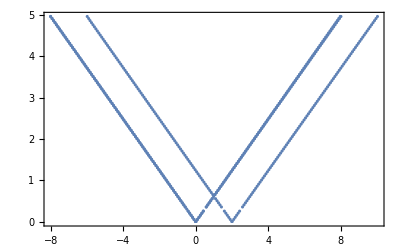

```mathematica
ListPlot[lld1,PlotRange->Full,Frame->True]
```

```mathematica
lld2=DisperMainK00np[pp,1/5,1/100,1,1/100];
```

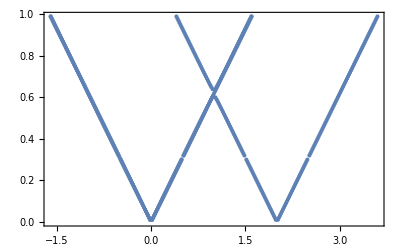

```mathematica
ListPlot[lld2,PlotRange->Full,Frame->True]
```

```mathematica
lld3=DisperMainK00np[pp,1/5,0.3085,0.3107,1/50000];
```

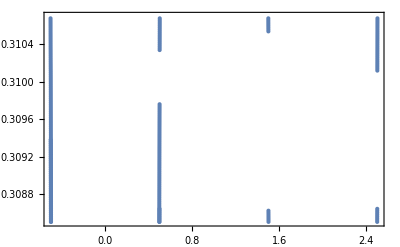

```mathematica
ListPlot[lld3,PlotRange->{All,{0.3085,0.3107}},Frame->True]
```

```mathematica
(*^^^^^^^^^-p=2-^^^^^^^^^*)
```

```mathematica
lld1=DisperMainK00np[pp,1/5,1/100,5,1/20];
```

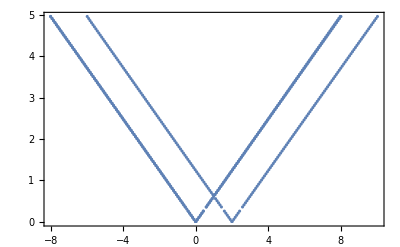

```mathematica
ListPlot[lld1,PlotRange->Full,Frame->True]
```

```mathematica
lld2=DisperMainK00np[pp,1/5,1/100,1,1/100];
```

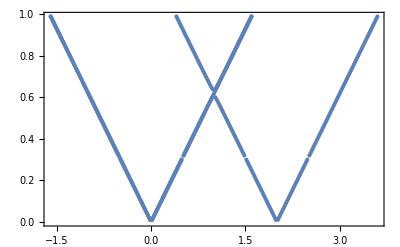

```mathematica
ListPlot[lld2,PlotRange->Full,Frame->True]
```

```mathematica
lld3=DisperMainK00np[pp,1/5,0.3085,0.3107,1/50000];
```

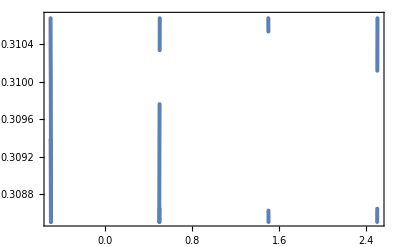

```mathematica
ListPlot[lld3,PlotRange->{All,{0.3085,0.3107}},Frame->True]
```

```mathematica
(*vvvvvvvv-p=3-vvvvvvvvv*)
```

```mathematica
DisperMainK00np[p_?IntegerQ,np1_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]
```

```mathematica
lld1=DisperMainK00np[pp,1/5,1/100,5,1/20];
```

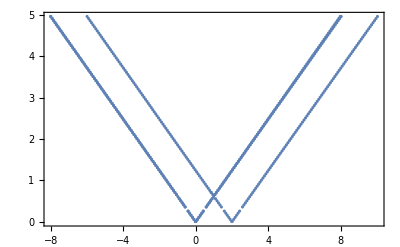

```mathematica
ListPlot[lld1,PlotRange->Full,Frame->True]
```

```mathematica
lld2=DisperMainK00np[pp,1/5,1/100,1,1/100];
```

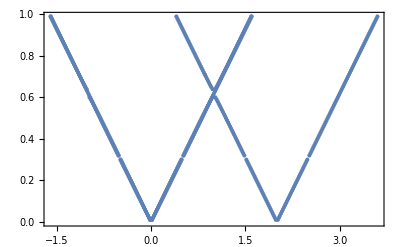

```mathematica
ListPlot[lld2,PlotRange->Full,Frame->True]
```

```mathematica
lld3=DisperMainK00np[pp,1/5,0.3085,0.3107,1/50000];
```

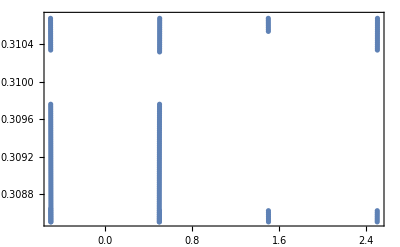

```mathematica
ListPlot[lld3,PlotRange->{All,{0.3085,0.3107}},Frame->True]
```

```mathematica
(*^^^^^^^^^-p=3-^^^^^^^^^*)
```

```mathematica
(*^^^+новое+^^^*)
```

```mathematica
(*старое*)
```

```mathematica
Branches[pp,3^2,1/5,1/3];//Timing
```

{0.71875,Null}

```mathematica
Length[Branches[pp,3^2,1/5,1/3]]
```

4

```mathematica
Branches[pp,3^2,1/5,1/5]
```

{{-3.14746+0. ⅈ,{-2.04955×10^-40+0. ⅈ,9.16342×10^-38+0. ⅈ,2.15045×10^-35+0. ⅈ,-9.59976×10^-33+0. ⅈ,-1.6605×10^-30+0. ⅈ,7.39377×10^-28+0. ⅈ,8.88566×10^-26+0. ⅈ,-3.93762×10^-23+0. ⅈ,-3.00405×10^-21+0. ⅈ,1.31653×10^-18+0. ⅈ,5.439×10^-17+0. ⅈ,-2.28813×10^-14+0. ⅈ,-3.48804×10^-13+0. ⅈ,3.38706×10^-10+0. ⅈ,-6.49127×10^-10+0. ⅈ,3.0666×10^-7+0. ⅈ,-3.11823×10^-6+0. ⅈ,0.0015484+0. ⅈ,-0.0147276+0. ⅈ,0.998437+0. ⅈ,0.0538874+0. ⅈ,-0.000126643+0. ⅈ,-2.75844×10^-6+0. ⅈ,6.27899×10^-9+0. ⅈ,7.63845×10^-11+0. ⅈ,-1.71997×10^-13+0. ⅈ,-1.3949×10^-15+0. ⅈ,3.73717×10^-17+0. ⅈ,-3.05229×10^-16+0. ⅈ,-1.34067×10^-16+0. ⅈ,1.90332×10^-16+0. ⅈ,5.44972×10^-17+0. ⅈ,4.44089×10^-16+0. ⅈ,7.28584×10^-17+0. ⅈ,0.+0. ⅈ,-8.56791×10^-17+0. ⅈ,3.16587×10^-17+0. ⅈ,5.45627×10^-18+0. ⅈ,7.15385×10^-17+0. ⅈ,2.848×10^-16+0. ⅈ}},{-1.12476+0. ⅈ,{-9.54289×10^-44+0. ⅈ,4.27081×10^-41+0. ⅈ,1.30747×10^-38+0. ⅈ,-5.84565×10^-36+0. ⅈ,-1.37623×10^-33+0. ⅈ,6.14375×10^-31+0. ⅈ,1.0667×10^-28+0. ⅈ,-4.7499×10^-26+0. ⅈ,-5.73441×10^-24+0. ⅈ,2.54136×10^-21+0. ⅈ,1.95022×10^-19+0. ⅈ,-8.54855×10^-17+0. ⅈ,-3.56135×10^-15+0. ⅈ,1.49975×10^-12+0. ⅈ,2.3231×10^-11+0. ⅈ,-2.48195×10^-8+0. ⅈ,4.39731×10^-8+0. ⅈ,-0.0000206864+0. ⅈ,0.000209443+0. ⅈ,-0.103931+0. ⅈ,0.994506+0. ⅈ,0.0124532+0. ⅈ,0.000681676+0. ⅈ,-1.60324×10^-6+0. ⅈ,-3.51971×10^-8+0. ⅈ,8.01325×10^-11+0. ⅈ,9.79998×10^-13+0. ⅈ,-1.46677×10^-15+0. ⅈ,2.44686×10^-17+0. ⅈ,-3.47101×10^-16+0. ⅈ,-2.02319×10^-16+0. ⅈ,2.09522×10^-16+0. ⅈ,-2.22045×10^-16+0. ⅈ,-1.44849×10^-16+0. ⅈ,5.55112×10^-17+0. ⅈ,-3.27898×10^-16+0. ⅈ,1.94289×10^-16+0. ⅈ,-2.75421×10^-17+0. ⅈ,-2.99856×10^-16+0. ⅈ,-6.00111×10^-17+0. ⅈ}},{3.12476+0. ⅈ,{-8.1402×10^-46+0. ⅈ,3.64744×10^-43+0. ⅈ,1.77253×10^-40+0. ⅈ,-7.9386×10^-38+0. ⅈ,-3.14625×10^-35+0. ⅈ,1.40819×10^-32+0. ⅈ,4.44412×10^-30+0. ⅈ,-1.98723×10^-27+0. ⅈ,-4.84416×10^-25+0. ⅈ,2.16302×10^-22+0. ⅈ,3.91177×10^-20+0. ⅈ,-1.74257×10^-17+0. ⅈ,-2.21027×10^-15+0. ⅈ,9.80324×10^-13+0. ⅈ,8.01325×10^-11+0. ⅈ,-3.51971×10^-8+0. ⅈ,-1.60324×10^-6+0. ⅈ,0.000681676+0. ⅈ,0.0124532+0. ⅈ,0.994506+0. ⅈ,-0.103931+0. ⅈ,0.000209443+0. ⅈ,-0.0000206864+0. ⅈ,4.39731×10^-8+0. ⅈ,-2.48195×10^-8+0. ⅈ,2.32328×10^-11+0. ⅈ,1.49987×10^-12+0. ⅈ,-3.72332×10^-15+0. ⅈ,-7.20326×10^-17+0. ⅈ,-9.29267×10^-18+0. ⅈ,5.06074×10^-17+0. ⅈ,1.47106×10^-16+0. ⅈ,0.+0. ⅈ,-1.31839×10^-16+0. ⅈ,0.+0. ⅈ,-1.60191×10^-16+0. ⅈ,2.50722×10^-18+0. ⅈ,-4.37669×10^-18+0. ⅈ,3.52532×10^-16+0. ⅈ,5.25196×10^-17+0. ⅈ}},{5.14746+0. ⅈ,{-2.37112×10^-49+0. ⅈ,1.06282×10^-46+0. ⅈ,6.22478×10^-44+0. ⅈ,-2.78919×10^-41+0. ⅈ,-1.35843×10^-38+0. ⅈ,6.08401×10^-36+0. ⅈ,2.41712×10^-33+0. ⅈ,-1.08186×10^-30+0. ⅈ,-3.42361×10^-28+0. ⅈ,1.53092×10^-25+0. ⅈ,3.74355×10^-23+0. ⅈ,-1.67161×10^-20+0. ⅈ,-3.03416×10^-18+0. ⅈ,1.35167×10^-15+0. ⅈ,1.72207×10^-13+0. ⅈ,-7.63843×10^-11+0. ⅈ,-6.27899×10^-9+0. ⅈ,2.75844×10^-6+0. ⅈ,0.000126643+0. ⅈ,-0.0538874+0. ⅈ,-0.998437+0. ⅈ,0.0147276+0. ⅈ,-0.0015484+0. ⅈ,3.11823×10^-6+0. ⅈ,-3.0666×10^-7+0. ⅈ,6.49127×10^-10+0. ⅈ,-3.38706×10^-10+0. ⅈ,3.44391×10^-13+0. ⅈ,2.25301×10^-14+0. ⅈ,-4.37622×10^-16+0. ⅈ,-1.05766×10^-16+0. ⅈ,-2.35283×10^-16+0. ⅈ,-2.22045×10^-16+0. ⅈ,1.22298×10^-16+0. ⅈ,-4.85723×10^-17+0. ⅈ,1.55251×10^-16+0. ⅈ,1.5748×10^-16+0. ⅈ,1.29518×10^-17+0. ⅈ,3.44357×10^-17+0. ⅈ,-1.33809×10^-16+0. ⅈ}}}

```mathematica
Table[{1,2},{ii,1,3}]//MatrixForm
```

(1 | 2
1 | 2
1 | 2)

```mathematica
yy=2;
```

```mathematica
f=Compile[{{t,_Real}},Evaluate[yy+2 t],CompilationOptions->{"ExpressionOptimization"->True}];
```

```mathematica
CompilePrint[f]
```

1 argument
		1 Integer register
		3 Real registers
		Underflow checking off
		Overflow checking off
		Integer overflow checking on
		RuntimeAttributes -> {}

		R0 = A1
		I0 = 2
		Result = R2

1	R1 = I0
2	R1 = R1 * R0
3	R2 = I0
4	R2 = R2 + R1
5	Return

```mathematica
f[1]
```

4.

```mathematica
(*vvvvvvvv+p=3+vvvvvvvvvv*)
```

```mathematica
ll2=DisperMain[pp,1/3,1/5,1/100,5,1/20];
```

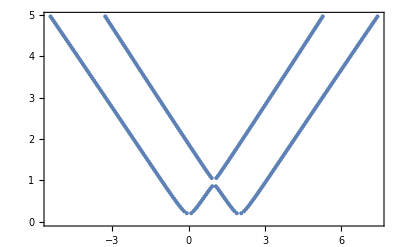

```mathematica
ListPlot[ll2,PlotRange->Full,Frame->True]
```

```mathematica
ll21=DisperSimpl[1/3,1/5,1/100,5,1/20];
```

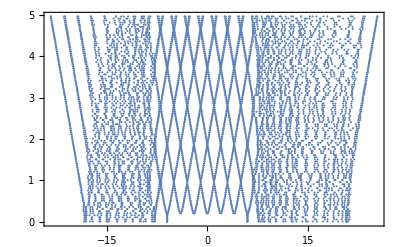

```mathematica
ListPlot[ll21,PlotRange->Full,Frame->True]
```

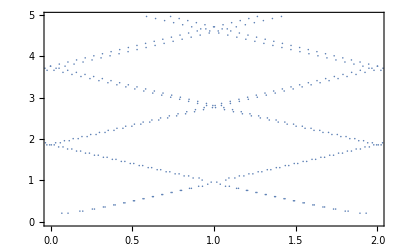

```mathematica
ListPlot[ll21,PlotRange->{{0,2},All},Frame->True]
```

```mathematica
ll3=DisperMain[pp,1/3,1/3,1/5,3/2,1/400];
```

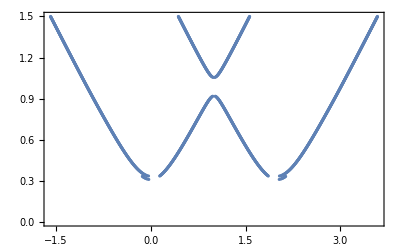

```mathematica
ListPlot[ll3,PlotRange->Full,Frame->True]
```

```mathematica
ll4=DisperMain[pp,1/3,1/3,1/5,2/5,1/3000];
```

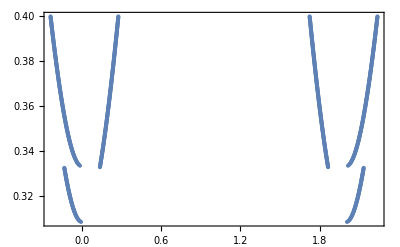

```mathematica
ListPlot[ll4,PlotRange->Full,Frame->True]
```

```mathematica
(*^^^^^^+p=3+^^^^^^^^^^*)
```

```mathematica
(*vvvvvvv+p=4+vvvvvvvv*)
```

```mathematica
ll2=DisperMain[pp,1/3,1/5,1/100,5,1/20];
```

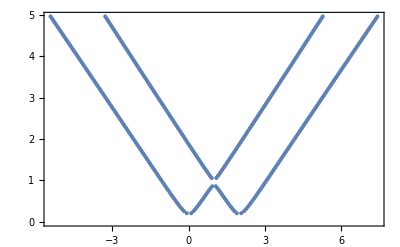

```mathematica
ListPlot[ll2,PlotRange->Full,Frame->True]
```

```mathematica
ll3=DisperMain[pp,1/3,1/3,1/5,3/2,1/400];
```

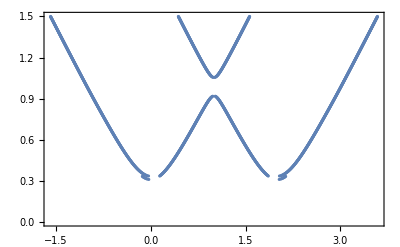

```mathematica
ListPlot[ll3,PlotRange->Full,Frame->True]
```

```mathematica
ll31=MapAt[Mod[#,2]&,ll3,{1;;Length[ll3],1}];
```

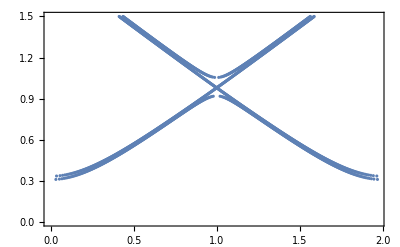

```mathematica
ListPlot[ll31,PlotRange->Full,Frame->True]
```

```mathematica
ll4=DisperMain[pp,1/3,1/3,1/5,2/5,1/3000];
```

```mathematica
ListPlot[ll4,PlotRange->Full,Frame->True]
```

-Graphics-

```mathematica
ll5=DisperMain[pp,-1/3,1/5,1/100,5,1/20];
```

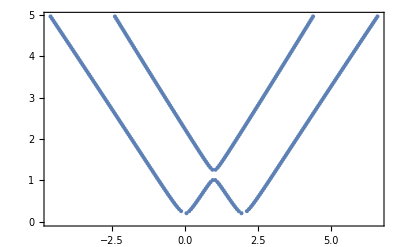

```mathematica
ListPlot[ll5,PlotRange->Full,Frame->True]
```

```mathematica
ll6=DisperMain[pp,-1/3,1/3,1/5,3/2,1/400];
```

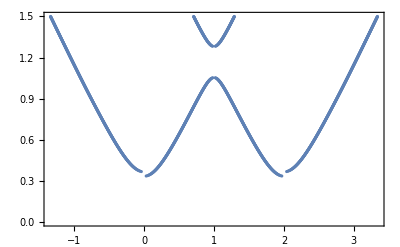

```mathematica
ListPlot[ll6,PlotRange->Full,Frame->True]
```

```mathematica
ll7=DisperMain[pp,-1/3,1/3,3/10,45/100,1/3000];
```

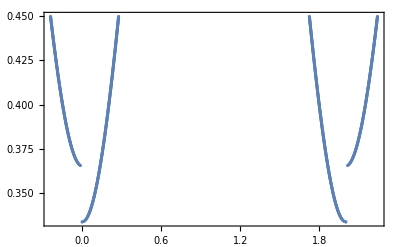

```mathematica
ListPlot[ll7,PlotRange->Full,Frame->True]
```

```mathematica
ll10=DisperMain[pp,-1/3,1/50,1/2000,2,1/200];
```

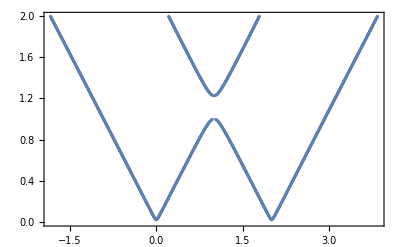

```mathematica
ListPlot[ll10,PlotRange->Full,Frame->True]
```

```mathematica
ll11=DisperMain[pp,-1/3,1/50,1/2000,2/10,1/400];
```

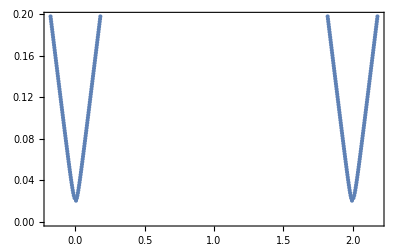

```mathematica
ListPlot[ll11,PlotRange->Full,Frame->True]
```

```mathematica
ll8=DisperMain[pp,1/3,2,18/10,24/10,1/2000];
```

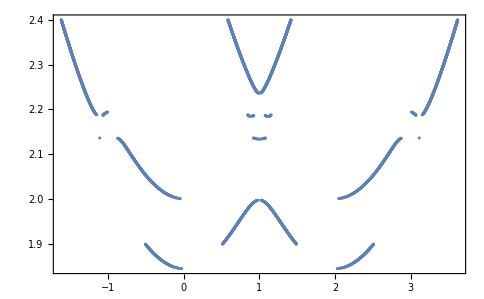

```mathematica
ListPlot[ll8,PlotRange->Full,Frame->True]
```

```mathematica
Mod[-5.1,2]
```

0.9

```mathematica
ll81=MapAt[Mod[#,2]&,ll8,{1;;Length[ll8],1}];
```

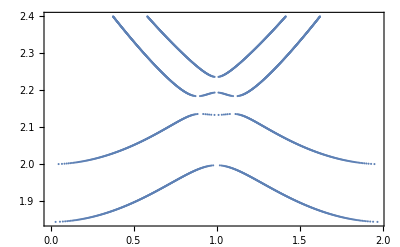

```mathematica
ListPlot[ll81,PlotRange->Full,Frame->True]
```

```mathematica
2 Sqrt[1+1/3]//N
```

2.3094

```mathematica
ArcSin[2/2.15]
ArcSin[2/2.15] 180/Pi
```

1.19505

68.4711

```mathematica
ll9=DisperMain[pp,1/3,2,12/10,3,1/1000];
```

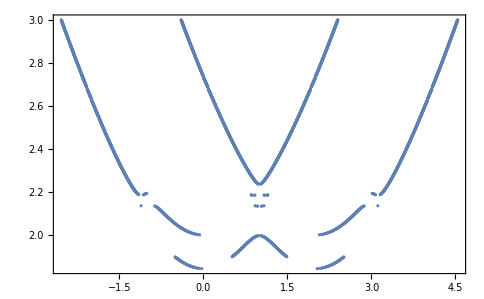

```mathematica
ListPlot[ll9,PlotRange->Full,Frame->True]
```

```mathematica
ll12=DisperMain[pp,-1/3,2,1,3,1/1000];
```

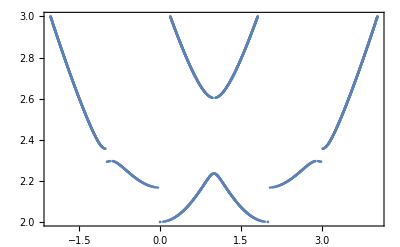

```mathematica
ListPlot[ll12,PlotRange->Full,Frame->True]
```

```mathematica
ll121=MapAt[Mod[#,2]&,ll12,{1;;Length[ll12],1}];
```

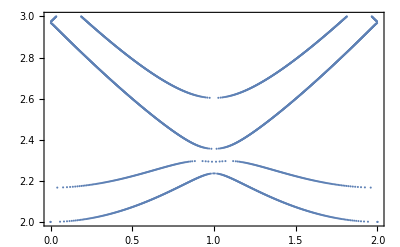

```mathematica
ListPlot[ll121,PlotRange->Full,Frame->True]
```

```mathematica
ll13=DisperMain[pp,-1/3,20,1,25,1/1000];
```

$Aborted[]

```mathematica
ll13=DisperMain[pp,-1/3,20,1,25,1/20];
```

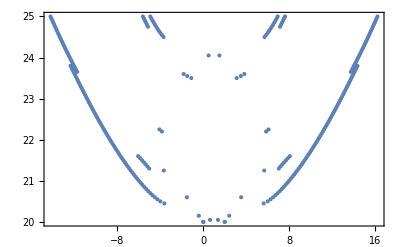

```mathematica
ListPlot[ll13,PlotRange->Full,Frame->True]
```

```mathematica
ll131=MapAt[Mod[#,2]&,ll13,{1;;Length[ll13],1}];
```

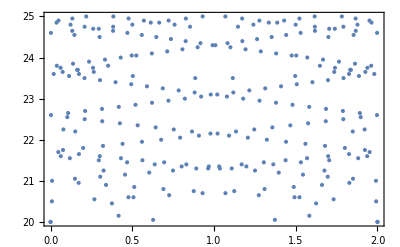

```mathematica
ListPlot[ll131,PlotRange->Full,Frame->True]
```

```mathematica
ll14=DisperMain[pp,-1/3,20,18,25,1/500];
```

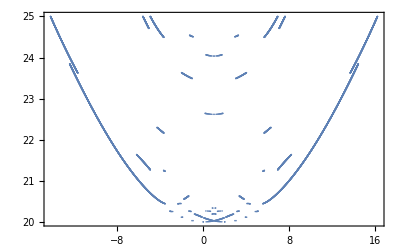

```mathematica
ListPlot[ll14,PlotRange->Full,Frame->True]
```

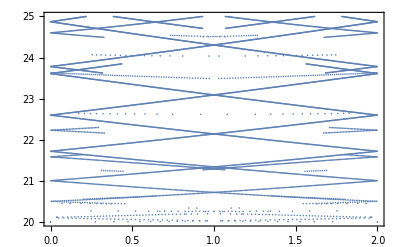

```mathematica
ListPlot[MapAt[Mod[#,2]&,ll14,{1;;Length[ll14],1}],PlotRange->Full,Frame->True]
```

```mathematica
ll15=DisperMain[pp,-1/3,20,18,206/10,1/4000];
```

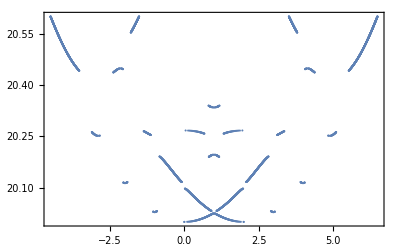

```mathematica
ListPlot[ll15,PlotRange->Full,Frame->True]
```

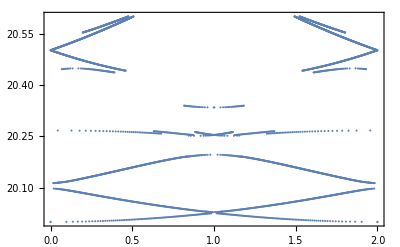

```mathematica
ListPlot[MapAt[Mod[#,2]&,ll15,{1;;Length[ll15],1}],PlotRange->Full,Frame->True]
```

```mathematica
20/Sqrt[1-1/3]//N
```

24.4949

```mathematica
ll16=DisperMain[pp,1/3,20,17,25,1/200];
```

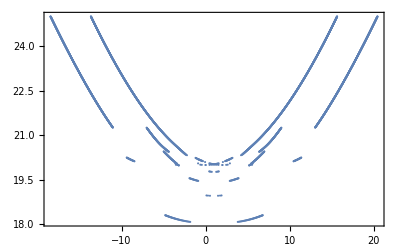

```mathematica
ListPlot[ll16,PlotRange->Full,Frame->True]
```

```mathematica
ll17=DisperMain[pp,1/3,20,17,215/10,1/500];
```

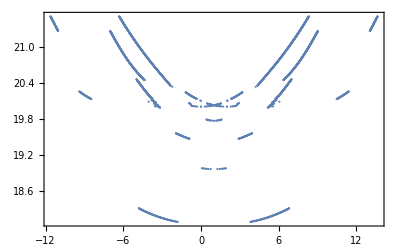

```mathematica
ListPlot[ll17,PlotRange->Full,Frame->True]
```

```mathematica
20/Sqrt[1+1/3]//N
```

17.3205

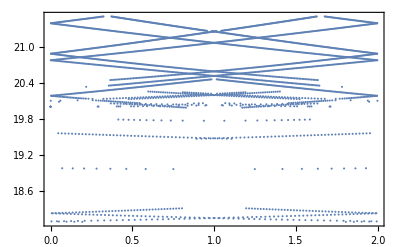

```mathematica
ListPlot[MapAt[Mod[#,2]&,ll17,{1;;Length[ll17],1}],PlotRange->Full,Frame->True]
```

```mathematica
ll18=DisperMain[pp,1/3,20,173/10,20,1/10000];
```

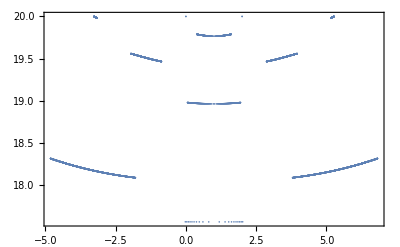

```mathematica
ListPlot[ll18,PlotRange->Full,Frame->True]
```

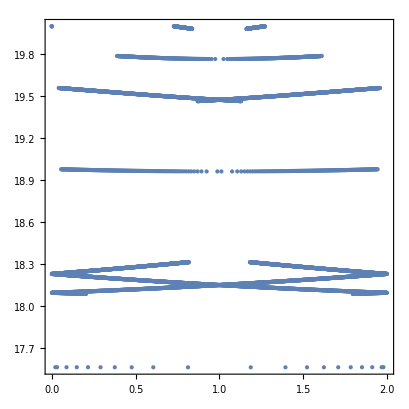

```mathematica
ListPlot[MapAt[Mod[#,2]&,ll18,{1;;Length[ll18],1}],PlotRange->Full,Frame->True,AspectRatio->1,PlotStyle->PointSize[Tiny]]
```

```mathematica
(*^^^^^^+p=4+^^^^^^^^^^*)
```

```mathematica
(*vvvvvvv+p=5+vvvvvvv*)
```

```mathematica
ll19=DisperMain[pp,1/3,20,173/10,20,1/10000];
```

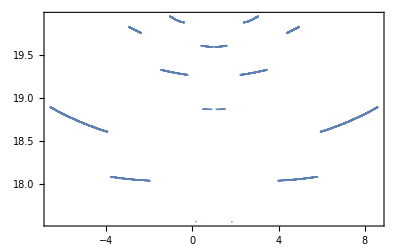

```mathematica
ListPlot[ll19,PlotRange->Full,Frame->True]
```

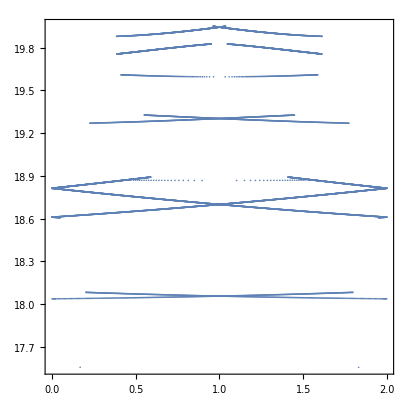

```mathematica
ListPlot[MapAt[Mod[#,2]&,ll19,{1;;Length[ll19],1}],PlotRange->Full,Frame->True,AspectRatio->1]
```

```mathematica
(*^^^^^^+p=5+^^^^^^^^^^*)
```

```mathematica
(*vvvvvvv+p=6+vvvvvvv*)
```

```mathematica
ll20=DisperMain[pp,1/3,20,173/10,20,1/10000];
```

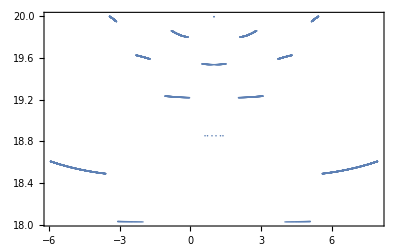

```mathematica
ListPlot[ll20,PlotRange->Full,Frame->True]
```

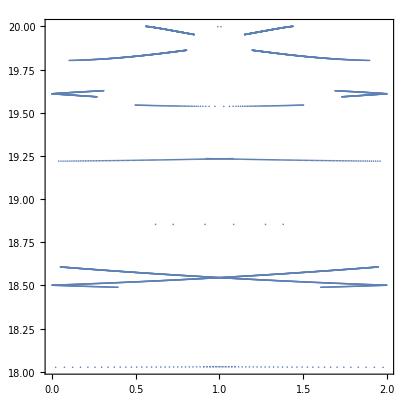

```mathematica
ListPlot[MapAt[Mod[#,2]&,ll20,{1;;Length[ll20],1}],PlotRange->Full,Frame->True,AspectRatio->1]
```

```mathematica
(*^^^^^^+p=6+^^^^^^^^^^*)
```

```mathematica
(*vvvvvvv+p=7+vvvvvvv*)
```

```mathematica
ll21=DisperMain[pp,1/3,20,173/10,20,1/10000];
```

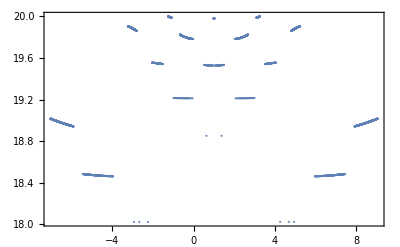

```mathematica
ListPlot[ll21,PlotRange->Full,Frame->True]
```

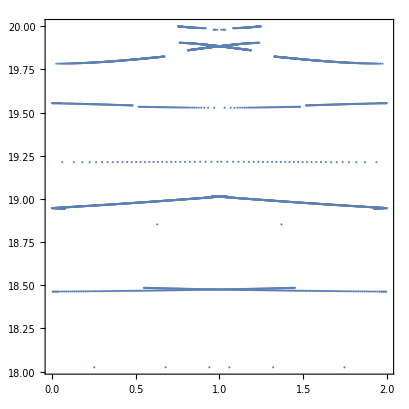

```mathematica
ListPlot[MapAt[Mod[#,2]&,ll21,{1;;Length[ll21],1}],PlotRange->Full,Frame->True,AspectRatio->1]
```

```mathematica
(*^^^^^^+p=7+^^^^^^^^^^*)
```

```mathematica
(*vvvvvvv+p=8+vvvvvvv*)
```

```mathematica
ll22=DisperMain[pp,1/3,20,173/10,20,1/10000];
```

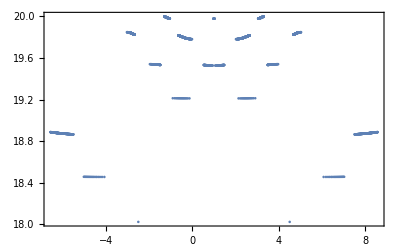

```mathematica
ListPlot[ll22,PlotRange->Full,Frame->True]
```

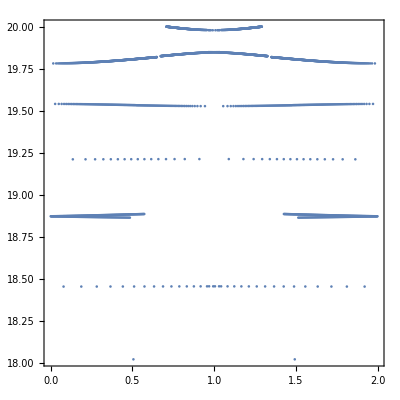

```mathematica
ListPlot[MapAt[Mod[#,2]&,ll22,{1;;Length[ll22],1}],PlotRange->Full,Frame->True,AspectRatio->1]
```

```mathematica
(*^^^^^^+p=8+^^^^^^^^^^*)
```

```mathematica
(*vvvvvvv+p=9+vvvvvvv*)
```

```mathematica
ll2=DisperMain[pp,1/3,1/5,1/100,5,1/20];//Timing
```

{4.94523,Null}

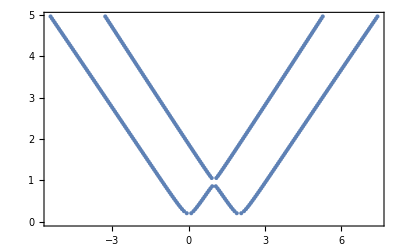

```mathematica
ListPlot[ll2,PlotRange->Full,Frame->True]
```

```mathematica
ll23=DisperMain[pp,1/3,20,173/10,20,1/10000];
```

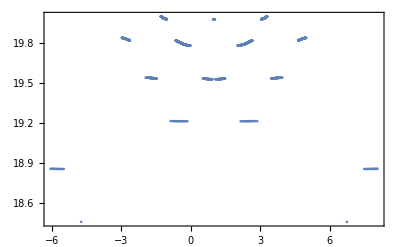

```mathematica
ListPlot[ll23,PlotRange->Full,Frame->True]
```

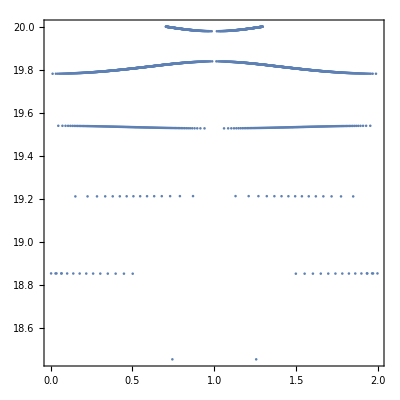

```mathematica
ListPlot[MapAt[Mod[#,2]&,ll23,{1;;Length[ll23],1}],PlotRange->Full,Frame->True,AspectRatio->1]
```

```mathematica
Length[ll23]
```

1878

```mathematica
(*^^^^^^+p=9+^^^^^^^^^^*)
```

```mathematica
(*vvvvvvv+p=10+vvvvvvv*)
```

```mathematica
ll24=DisperMain[pp,1/3,20,173/10,20,1/10000];
```

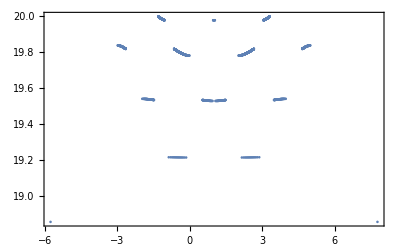

```mathematica
ListPlot[ll24,PlotRange->Full,Frame->True]
```

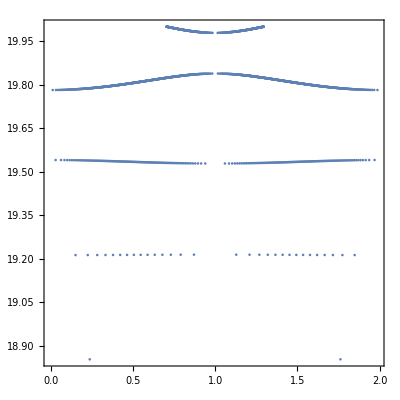

```mathematica
ListPlot[MapAt[Mod[#,2]&,ll24,{1;;Length[ll24],1}],PlotRange->Full,Frame->True,AspectRatio->1]
```

```mathematica
Length[ll24]
```

1840

```mathematica
ll24s=DisperSimpl3[1/3,20,173/10,20,1/10000];
```

```mathematica
Length[ll24s]
```

189010

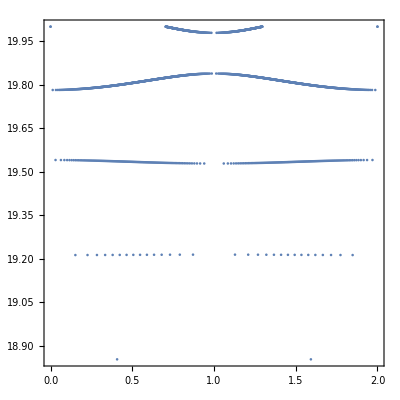

```mathematica
ListPlot[Select[ll24s,((#[[1]]≤2)&&(#[[1]]≥0))&],PlotRange->Full,Frame->True,AspectRatio->1]
```

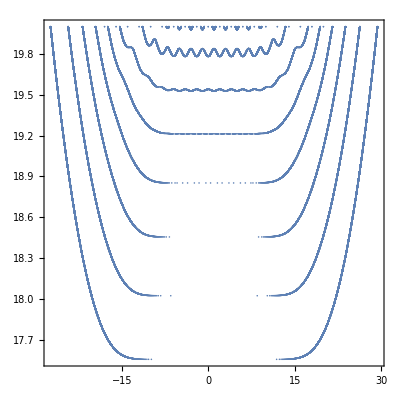

```mathematica
ListPlot[ll24s,PlotRange->Full,Frame->True,AspectRatio->1]
```

```mathematica
(*машинная точность *)
```

```mathematica
ll25s=DisperSimplN[1/3,20,17.3,20.,0.0001];
```

```mathematica
Length[ll25s]
```

86402

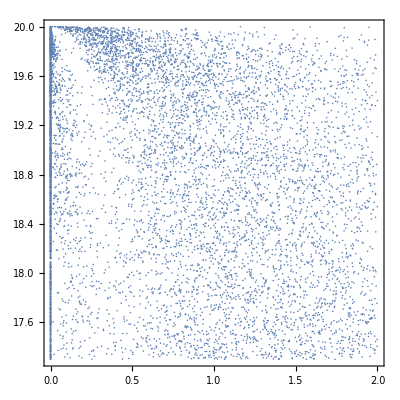

```mathematica
ListPlot[Select[ll25s,((#[[1]]≤2)&&(#[[1]]≥0))&],PlotRange->Full,Frame->True,AspectRatio->1]
```

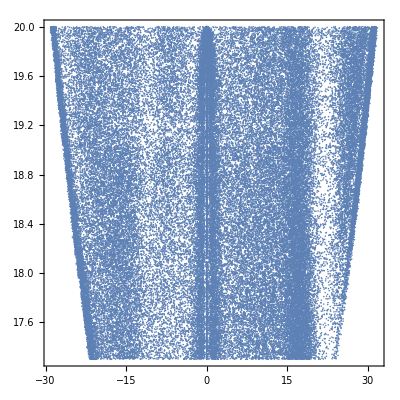

```mathematica
ListPlot[ll25s,PlotRange->Full,Frame->True,AspectRatio->1]
```

```mathematica
(*^^^^^^+p=10+^^^^^^^^^^*)
```

```mathematica
NullSpace[{{1,0},{0,0}}][[1]]
NullSpace[{{1,0},{0,0}}][[1,1]]
NullSpace[{{1,0},{0,0}}][[1,2]]
```

{0,1}

0

1

```mathematica
qn/.{qn->1}
```

1

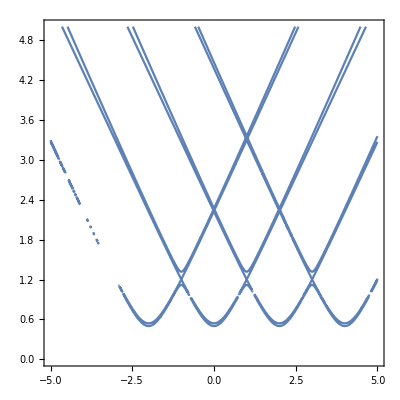

```mathematica
ContourPlot[(dsp1/.{de->-0.3,kp->1/2,k0s->kt^2})==0,{qn,-5,5},{kt,0,5},PlotPoints->50]
```

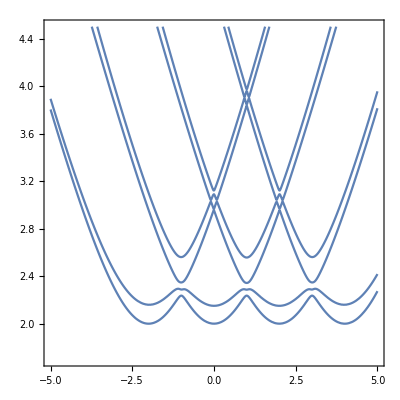

```mathematica
ContourPlot[(dsp1/.{de->-0.3,kp->2,k0s->kt^2})==0,{qn,-5,5},{kt,1.7,4.5},PlotPoints->70]
```

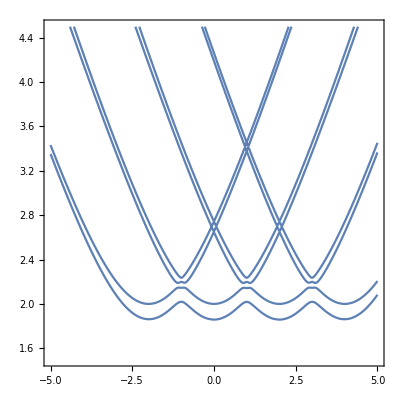

```mathematica
ContourPlot[(dsp1/.{de->0.3,kp->2,k0s->kt^2})==0,{qn,-5,5},{kt,1.5,4.5},PlotPoints->50]
```

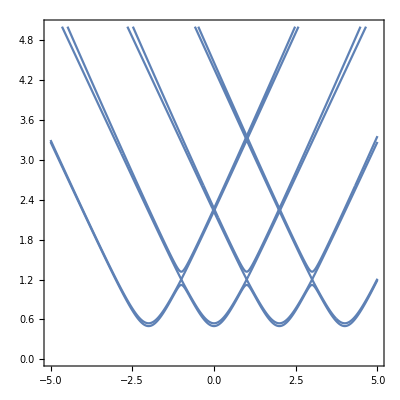

```mathematica
ContourPlot[(dsp1/.{de->-0.3,kp->1/2,k0s->kt^2})==0,{qn,-5,5},{kt,0,5},PlotPoints->500]
```

```mathematica
(*vvvvvv+мусор+vvvvvvvv*)
```

```mathematica
dsp2=Collect[Det[mmi[3]],qn,Simplify];
```

```mathematica
dsp22=dsp2/.{de->0.3,kp->1/2,k0s->4}
```

qn^24-24 qn^23+84.025 qn^22+2199.45 qn^21-18640.4 qn^20-48459. qn^19+962230. qn^18-1.08339×10^6 qn^17-2.17413×10^7 qn^16+6.36292×10^7 qn^15+2.29551×10^8 qn^14-1.09019×10^9 qn^13-8.83889×10^8 qn^12+8.9711×10^9 qn^11-2.35443×10^9 qn^10-3.87409×10^10 qn^9+3.10346×10^10 qn^8+8.4782×10^10 qn^7-9.45043×10^10 qn^6-7.46139×10^10 qn^5+9.8131×10^10 qn^4+8.57618×10^8 qn^3-1.1297×10^9 qn^2-2.18503×10^6 qn+2.8795×10^6

```mathematica
dspr=NRoots[dsp22==0,qn]
```

qn==-6.09007∨qn==-6.07879∨qn==-4.08841∨qn==-4.06161∨qn==-2.08841∨qn==-2.06161∨qn==-1.93858∨qn==-1.91794∨qn==-0.088414∨qn==-0.0616126∨qn==0.0616126∨qn==0.088414∨qn==1.91159∨qn==1.93839∨qn==2.06161∨qn==2.08841∨qn==3.91794∨qn==3.93858∨qn==4.06161∨qn==4.08841∨qn==6.06161∨qn==6.08841∨qn==8.07879∨qn==8.09007

```mathematica
ll=qn/.{ToRules[dspr]}
```

{-6.09007,-6.07879,-4.08841,-4.06161,-2.08841,-2.06161,-1.93858,-1.91794,-0.088414,-0.0616126,0.0616126,0.088414,1.91159,1.93839,2.06161,2.08841,3.91794,3.93858,4.06161,4.08841,6.06161,6.08841,8.07879,8.09007}

```mathematica
Select[ll,(#∈Reals)&]
Sort[ll]
ll[[1]]
```

{-6.09007,-6.07879,-4.08841,-4.06161,-2.08841,-2.06161,-1.93858,-1.91794,-0.088414,-0.0616126,0.0616126,0.088414,1.91159,1.93839,2.06161,2.08841,3.91794,3.93858,4.06161,4.08841,6.06161,6.08841,8.07879,8.09007}

{-6.09007,-6.07879,-4.08841,-4.06161,-2.08841,-2.06161,-1.93858,-1.91794,-0.088414,-0.0616126,0.0616126,0.088414,1.91159,1.93839,2.06161,2.08841,3.91794,3.93858,4.06161,4.08841,6.06161,6.08841,8.07879,8.09007}

-6.09007

```mathematica
Select[qn/.{ToRules[dspr]},(#≥0&&#<=2)&]
```

{0.0616126,0.088414,1.91159,1.93839}

```mathematica
d=DiagonalMatrix[{1,10^(-20),-2}];
t={{1,2,4},{2 I,3,2},{1,0,4}};
m=N[t.d.ConjugateTranspose[t]];
```

```mathematica
Det[t]
```

4-16 ⅈ

```mathematica
Eigensystem[m,Method->{"FEAST","Interval"->{-0.001,0.001}}]//RepeatedTiming
```

{0.0005,(-5.76539×10^-32
{0.682857+0.183593 ⅈ,6.924×10^-17+1.72616×10^-17 ⅈ,-0.682857-0.183593 ⅈ})}

```mathematica
ee=Eigensystem[m,Method->{"FEAST","Interval"->{-0.001,0.001}}][[2]]
ee/Norm[ee]
Norm[ee/Norm[ee]]
```

(-0.424264+0.565685 ⅈ | -3.94991×10^-17+5.69306×10^-17 ⅈ | 0.424264-0.565685 ⅈ)

(-0.424264+0.565685 ⅈ | -3.94991×10^-17+5.69306×10^-17 ⅈ | 0.424264-0.565685 ⅈ)

1.

```mathematica
NullSpace[m]//RepeatedTiming
```

{0.0000114,(0.707099-0.00341182 ⅈ | -1.11022×10^-16+1.38778×10^-17 ⅈ | -0.707099+0.00341182 ⅈ)}

```mathematica
LinearSolve
```

```mathematica
en=NullSpace[m]/Norm[NullSpace[m]]
```

(0.707099-0.00341182 ⅈ | -1.11022×10^-16+1.38778×10^-17 ⅈ | -0.707099+0.00341182 ⅈ)

```mathematica
m.en[[1]]
m.ee[[1]]
```

{1.06581×10^-14+5.55112×10^-17 ⅈ,3.55271×10^-15-2.22045×10^-16 ⅈ,1.06581×10^-14+5.55112×10^-17 ⅈ}

{-1.77636×10^-15+0. ⅈ,0.+0. ⅈ,-1.77636×10^-15+0. ⅈ}

```mathematica
en[[1,1]]/ee[[1,1]]
en[[1,2]]/ee[[1,2]]
en[[1,3]]/ee[[1,3]]
```

-0.603853-0.797096 ⅈ

1.07791+1.20227 ⅈ

-0.603853-0.797096 ⅈ

```mathematica
dsp2/.{de->0.3,kp->1/2,k0s->kt^2}
```

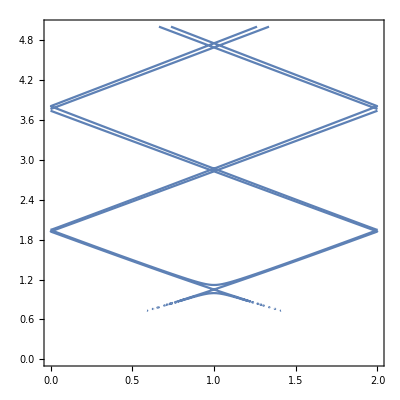

```mathematica
ContourPlot[(dsp2/.{de->0.3,kp->1/2,k0s->kt^2})==0,{qn,0,2},{kt,0,5},PlotPoints->100]
```

```mathematica
ContourPlot[(dsp2/.{de->0.3,kp->1/2,k0s->kt^2})==0,{qn,0,2},{kt,0,5},PlotPoints->100]
```

-Graphics-

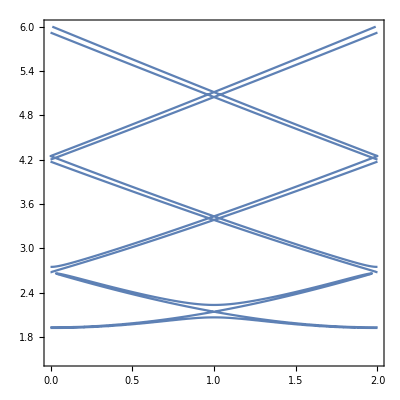

```mathematica
ContourPlot[(dsp2/.{de->0.3,kp->2,k0s->kt^2})==0,{qn,0,2},{kt,1.5,6},PlotPoints->100]
```